# B_c Mixing Angle: Coordinate-Space Calculation

This notebook is the independent coordinate-space workflow. It loads BcMixingCoordinate.wl only. Momentum-space comparisons are intentionally kept out of the main run so that coordinate-space results can be checked and quoted independently.

## Load Coordinate File

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Get["BcMixingCoordinate.wl"];
```

Loaded BcMixingCoordinate.wl. Run CoordinateCheckEnvironment[] for setup information.

```mathematica
CoordinateCheckEnvironment[]
```

<|FeynCalcLoaded→True,FeynCalcVersion→10.2.0,ImplementedOrders→{pert,G2c,G2b,G2local,pertG2local,G2gg,G2full,pertG2full,G3c,G3b,G3local,G3full,totalLocal,totalFull},NumericalOrders→{pert},ReducedLocalOrders→{G2c,G2b,G2local,G3c,G3b,G3local,pertG2local,totalLocal},IndependentPendingOrders→{G2c,G2b,G2local,G2gg,G2full,pertG2full,G3c,G3b,G3local,G3full,totalFull},ReducedLocalIntegrationAvailable→False,TensorCurrentScale→mb+mc,Threshold→(mb+mc)^2,DefaultParameters→<|mb→4.18,mc→1.27,G2→0.473741,G3→0.57,M2→10.,s0→55.|>,WangWindow→<|M2Range→{7.,9.},M2Values→{7.,8.,9.},s0Central→54.,s0Range→{53.,55.},s0Values→{53.,54.,55.}|>|>

```mathematica
CoordinateIndependenceStatus[] // Dataset
```

## Run Controls

```mathematica
m2Test = 8.0;
s0Test = 54.0;
coordinateOrder = "pert";
coordinateNPoints = 25;
coordinateYHalfWidth = 1.0;
commonThetaPlotRange = $BcCoordinateMomentumComparableThetaRange;
coordinateMonteCarloSamples = 50;
coordinateMonteCarloBins = 15;
coordinateExportPDF = False;
coordinateRunLocalDiagnostics = False;
```

For an independent coordinate-space paper, keep coordinateOrder = "pert" until the full coordinate-space G2 and G3 reductions are implemented. The local condensate bridge can be inspected by setting coordinateRunLocalDiagnostics = True, but that bridge is diagnostic only.

## Coordinate-Space Kernels

```mathematica
CoordinateSpectralDensityDerivationNote[]
```

Coordinate-space v1 uses the free heavy-quark propagator
S_Q(x)==(m_Q^2 (-(ⅈ γ.x 2m_Q √(-x^2))/x^2+(1m_Q √(-x^2))/(√(-x^2))))/(2 π)^2
The Fourier transform reduces to radial integrals with one J Bessel and two K Bessel functions.
The spectral density installed here is the perturbative result after the Huang-Liu/Azizi Bessel-Schwinger reduction.
Local single-line G2/G3 condensate checks are available through the reduced Borel bridge after loading BcMixingMomentum.wl.
The full coordinate-space G2 result still needs the open-field S^(G) S^(G) cross-line derivation.

```mathematica
CoordinateTraceKernel["AA", "pert"] // Short
```

(ⅈ «1» «1» (2 2mb r 2mc r (p̄·OverBar[«1»])^2+(«1»)^2 («1»+«1»)))/(4 π^4 r^4 (p̄)^2)

```mathematica
CoordinateTraceKernel["AB", "pert"] // Short
```

-(3 mb^2 mc^2 (1mc r 2mb r-1mb r 2mc r) (p̄·OverBar[xv]))/(4 (mb+mc) π^4 r^3)

```mathematica
CoordinateTraceKernel["BB", "pert"] // Short
```

(ⅈ «1» «1» (4 2mb r 2mc r (p̄·OverBar[«1»])^2+(«1»)^2 («1»-«1»)))/(4 (mb+mc)^2 π^4 r^4)

## Perturbative Spectral Densities

```mathematica
CoordinateSpectralDensity["AA", "pert", s] // Simplify // TraditionalForm
```

-(3 (mb^4+mb^2 (s-2 mc^2)+6 mb mc s+mc^4+mc^2 s-2 s^2) √(mb^4-2 mb^2 (mc^2+s)+(mc^2-s)^2))/(8 π^2 s^2)

```mathematica
CoordinateSpectralDensity["AB", "pert", s] // Simplify // TraditionalForm
```

(9 (mb-mc) (mb^2+2 mb mc+mc^2-s) √(mb^4-2 mb^2 (mc^2+s)+(mc^2-s)^2))/(8 π^2 s (mb+mc))

```mathematica
CoordinateSpectralDensity["BB", "pert", s] // Simplify // TraditionalForm
```

-(3 √(mb^4-2 mb^2 (mc^2+s)+(mc^2-s)^2) (2 mb^4-mb^2 (4 mc^2+s)+6 mb mc s+2 mc^4-mc^2 s-s^2))/(8 π^2 s (mb+mc)^2)

## Central Values

```mathematica
CoordinateNumericOPESummary[m2Test, s0Test, coordinateOrder] // Dataset
```

```mathematica
<|
  "M2" -> m2Test,
  "s0" -> s0Test,
  "Order" -> coordinateOrder,
  "ThetaDeg" -> CoordinateNumericMixingAngleDegrees[m2Test, s0Test, coordinateOrder]
|> // Dataset
```

```mathematica
CoordinateNumericMixingAngleDegrees[m2Test, s0Test, coordinateOrder]
```

43.2894

## Local Condensate Diagnostics

These cells are not independent full-OPE coordinate results. They are kept only as diagnostics while the coordinate-space G2gg, G2full, and G3full reductions are being derived.

```mathematica
If[TrueQ[coordinateRunLocalDiagnostics],
  CoordinateLocalCondensateSummary[m2Test, s0Test] // Dataset,
  "Local diagnostics skipped. Set coordinateRunLocalDiagnostics = True to inspect G2local/G3local."
]
```

Local diagnostics skipped. Set coordinateRunLocalDiagnostics = True to inspect G2local/G3local.

```mathematica
If[TrueQ[coordinateRunLocalDiagnostics],
  CoordinateNumericMixingAngleDegrees[m2Test, s0Test, "pertG2local"],
  "pertG2local skipped."
]
```

pertG2local skipped.

```mathematica
If[TrueQ[coordinateRunLocalDiagnostics],
  CoordinateNumericMixingAngleDegrees[m2Test, s0Test, "totalLocal", "IncludeG3" -> True],
  "totalLocal skipped."
]
```

totalLocal skipped.

## Wang-Window Stability: theta versus M2

```mathematica
coordM2Stability = CoordinateM2StabilityPublicationPlot[
  $BcCoordinateWangWindow["M2Range"],
  $BcCoordinateWangWindow["s0Values"],
  coordinateOrder,
  $BcCoordinateDefaultParameters,
  "NPoints" -> coordinateNPoints,
  "YHalfWidth" -> coordinateYHalfWidth,
  PlotRange -> {$BcCoordinateWangWindow["M2Range"], commonThetaPlotRange}
];
```

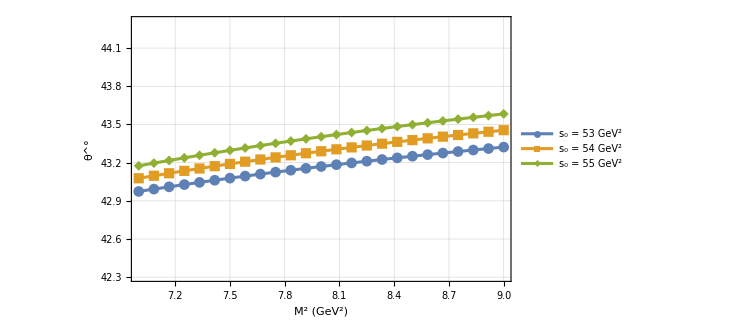

```mathematica
coordM2Stability["Plot"]
```

```mathematica
CoordinateExportStabilityDataCSV[coordM2Stability["Data"], "BcMixingCoordinateThetaVsM2_WangWindow.csv", "M2"]
```

BcMixingCoordinateThetaVsM2_WangWindow.csv

## Wang-Window Stability: theta versus s0

```mathematica
coordS0Stability = CoordinateS0StabilityPublicationPlot[
  $BcCoordinateWangWindow["s0Range"],
  $BcCoordinateWangWindow["M2Values"],
  coordinateOrder,
  $BcCoordinateDefaultParameters,
  "NPoints" -> coordinateNPoints,
  "YHalfWidth" -> coordinateYHalfWidth,
  PlotRange -> {$BcCoordinateWangWindow["s0Range"], commonThetaPlotRange}
];
```

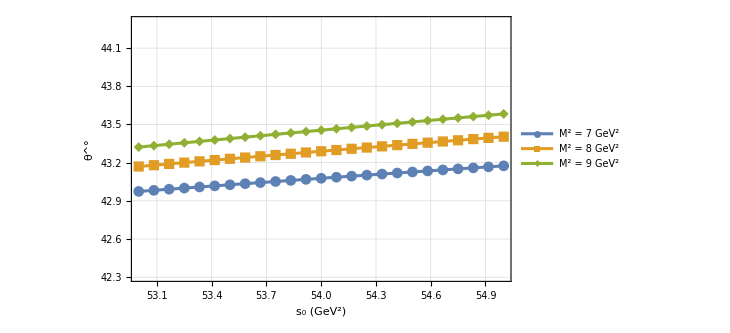

```mathematica
coordS0Stability["Plot"]
```

```mathematica
CoordinateExportStabilityDataCSV[coordS0Stability["Data"], "BcMixingCoordinateThetaVsS0_WangWindow.csv", "s0"]
```

BcMixingCoordinateThetaVsS0_WangWindow.csv

## Optional Stability PDF Export

```mathematica
If[TrueQ[coordinateExportPDF],
  {
    Export["BcMixingCoordinateThetaVsM2_WangWindow.pdf", coordM2Stability["Plot"]],
    Export["BcMixingCoordinateThetaVsS0_WangWindow.pdf", coordS0Stability["Plot"]]
  },
  "PDF export skipped. Set coordinateExportPDF = True when ready."
]
```

PDF export skipped. Set coordinateExportPDF = True when ready.

## Independent Coordinate Monte Carlo

This uses CoordinateMonteCarloMixingAngleUncertainty, not the momentum-space Monte Carlo engine.

```mathematica
coordUncertainty = CoordinateMonteCarloMixingAngleUncertainty[
  coordinateMonteCarloSamples,
  $BcCoordinateDefaultUncertaintyRanges,
  coordinateOrder,
  "IncludeG3" -> False,
  "Seed" -> 1234,
  "Progress" -> True
];
```

Coordinate Monte Carlo sample 5/50

Coordinate Monte Carlo sample 10/50

Coordinate Monte Carlo sample 15/50

Coordinate Monte Carlo sample 20/50

Coordinate Monte Carlo sample 25/50

Coordinate Monte Carlo sample 30/50

Coordinate Monte Carlo sample 35/50

Coordinate Monte Carlo sample 40/50

Coordinate Monte Carlo sample 45/50

Coordinate Monte Carlo sample 50/50

```mathematica
coordUncertainty["Summary"] // Dataset
```

```mathematica
coordUncertainty["Diagnostic"]
```

No accepted numeric theta values for order "pert". First test CoordinateNumericMixingAngleDegrees[8, 54, "pert"]; use non-perturbative coordinate orders only after their independent reductions are implemented.

```mathematica
coordUncertainty["CoordinateIndependence"]
```

Independent coordinate-space result.

```mathematica
CoordinateMonteCarloMixingAnglePublicationHistogram[coordUncertainty, coordinateMonteCarloBins]
```

No accepted coordinate Monte Carlo samples. Check coordUncertainty["Diagnostic"] and try coordinateMonteCarloOrder = "pert".

```mathematica
CoordinateExportMonteCarloMixingAngleSamples[coordUncertainty, "BcMixingCoordinateMonteCarloSamples.csv"];
CoordinateExportMonteCarloMixingAngleSummary[coordUncertainty, "BcMixingCoordinateMonteCarloSummary.csv"];
```

## Independent Full-OPE Status

These orders are intentionally not evaluated yet. They will become the coordinate-space publication result only after the x-space open-field contractions and Bessel/radial reductions are derived independently.

```mathematica
CoordinateIndependenceStatus[] // Dataset
```

```mathematica
AssociationMap[CoordinateIndependentOrderAvailableQ, {"pert", "G2full", "totalFull"}] // Dataset
```

## Optional Momentum Comparison

Run this section only when you want a cross-check against the momentum calculation. Do not use it to produce coordinate-space paper-final numbers.

```mathematica
(*
Get["BcMixingMomentum.wl"];
Get["BcMixingCoordinate.wl"];
CoordinateCompareToMomentum[m2Test, s0Test]
*)
```